```mathematica
ZetaMatrix[g_Graph]:=Block[{},
FormulaGraphReverse2[FindFullFormula[g]]]
```

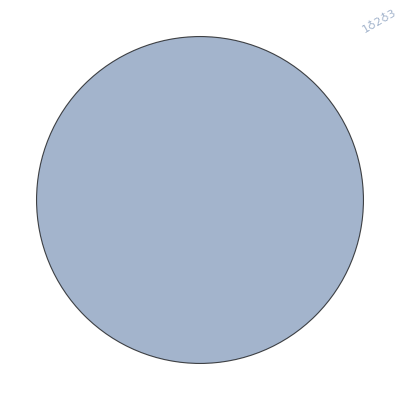

```mathematica
MobiusMatrix[CompleteGraph[3]]
```

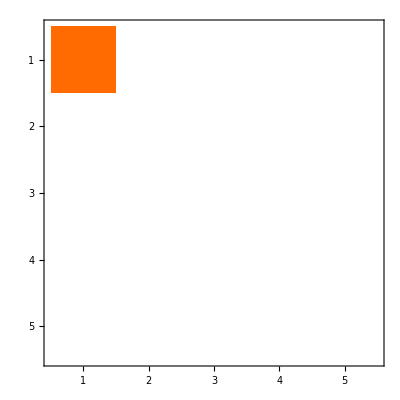

```mathematica
ZetaFunctionFromFormula[FindFullFormula[allGraphs5[alfa1Key,"graph"]]]//PseudoInverse//MatrixPlot
```

```mathematica
FindMpgEdges[g_]:=Select[EdgeList[g],MaximalPlanarQ[EdgeContract[g,#]]&]
```

```mathematica
FindMpgEdges[ReadGrof[30]]
```

{1<->2,1<->3,1<->7,1<->9,2<->6,2<->9,3<->7,3<->8,4<->5,4<->6,4<->8,5<->7,5<->9,7<->9}

```mathematica
Clear[ReplaceSymbol]
```

```mathematica
ReplaceSymbol[s_Symbol,edge_]:=Block[{b=SymbolToSets[s],both={edge[[1]],edge[[2]]}},
b=Map[(Map[If[MemberQ[both,#],both,#]&,#])&,b];
b=Map[DeleteDuplicates[Flatten[#]]&,b];
b=Sort[Map[Sort,b],#1[[1]]<#2[[1]]&];
SetsToSymbol[b]
]
```

```mathematica
ReplaceSymbol[s_List,edge_]:=Map[ReplaceSymbol[#,edge]&,s]
```

```mathematica
ReplaceSymbol[{x5x2x34},4<->1]
```

x5x2x34   4<->1

{v134x2x5}

```mathematica
MpgReduce[g_,edge_]:=Block[{contract,result},
contract=EdgeContract[g,edge];
result=
If[CompleteGraphQ[g],
{},
Join[{{edge,FindFullFormula[contract]}},
MpgReduce[contract]
]
];
result
]
```

```mathematica
MpgReduce[g_]:=Block[{edge=First[FindMpgEdges[g]], result},
result=
If[CompleteGraphQ[g],
{},
Join[{{{},FindFullFormula[g]}},
MpgReduce[g,edge]
]
];444444444444444444444444444444444444444444444444444444444444444444444444444444444444444444444444444444444444444444444
Table[
If[row=={},row,{row[[1]],ReplaceSymbol[row[[2]],edge]}]
,{row,result}
]
]
```

```mathematica
Map[{#[[1]],Framed[Multicolum4n[Map[SymbolToLabel,#[[2]]],4]]}&,MpgReduce[ReadGrof[6]]]//TableForm
```

| Multicolum4n[{12♁12♁3♁4♁5♁6♁7,12♁12♁3♁47♁5♁6,12♁12♁37♁4♁5♁6,124♁12♁3♁5♁6♁7,124♁12♁37♁5♁6,125♁12♁3♁4♁6♁7,125♁12♁3♁47♁6,125♁12♁37♁4♁6,12♁124♁3♁5♁6♁7,12♁124♁37♁5♁6,125♁124♁3♁6♁7,125♁124♁37♁6,12♁126♁3♁4♁5♁7,12♁126♁3♁47♁5,12♁126♁37♁4♁5,124♁126♁3♁5♁7,124♁126♁37♁5,125♁126♁3♁4♁7,125♁126♁3♁47,125♁126♁37♁4},4]
1<->2 | Multicolum4n[{12♁3♁4♁5♁6♁7,124♁3♁5♁6♁7,12♁3♁47♁5♁6,12♁37♁4♁5♁6,124♁37♁5♁6},4]
 | Multicolum4n[{12♁34♁34♁5♁6♁7,1234♁34♁5♁6♁7,12♁34♁347♁5♁6,12♁347♁34♁5♁6,1234♁347♁5♁6},4]
3<->4 | Multicolum4n[{12♁34♁5♁6♁7,12♁347♁5♁6},4]
 | Multicolum4n[{12♁34♁57♁57♁6,12♁3457♁57♁6},4]
5<->7 | Multicolum4n[{12♁34♁57♁6},4]

```mathematica
44444444444444444444444444444444444444444444444444444444444444444444444444444444444444444444444444444444444444
```

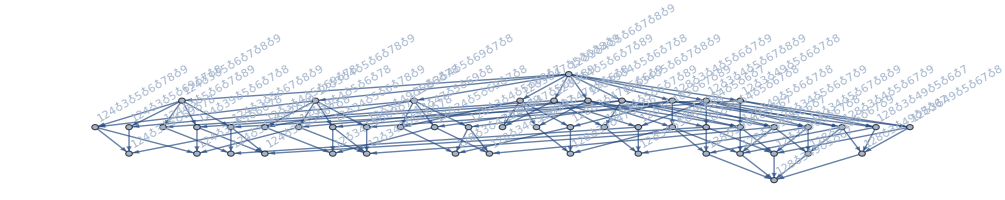
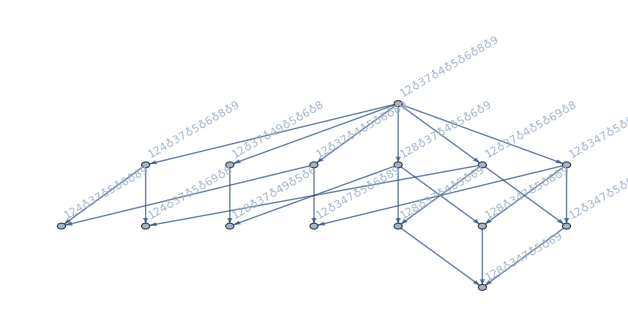
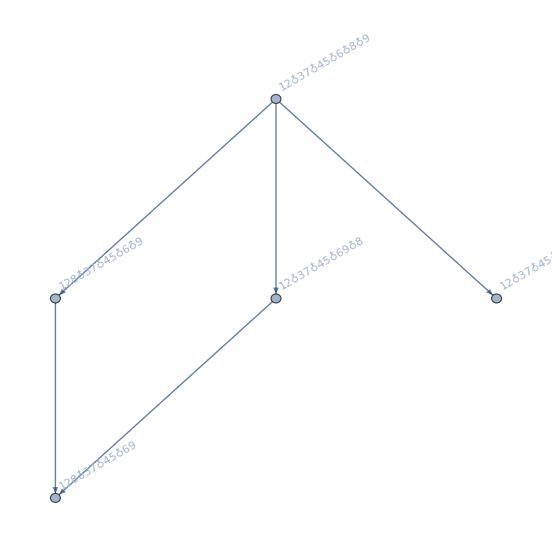
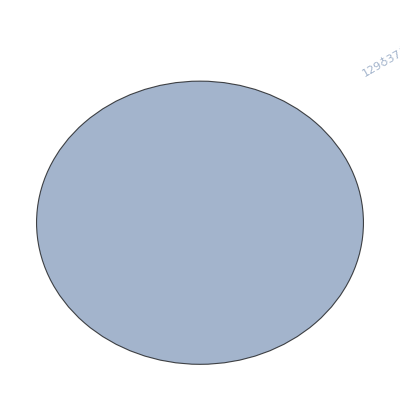
1<->2 | -Graphics-
3<->7 | -Graphics-
4<->5 | -Graphics-
6<->8 | -Graphics-
1<->9 | -Graphics-

```mathematica
Map[{#[[1]],Framed[FormulaGraphReverse2[#[[2]]]]}&,MpgReduce[ReadGrof[30]]]//TableForm
```

```mathematica
HexEdge[e_]:=IntegerString[e[[1]],16]<->IntegerString[e[[2]],16]
```

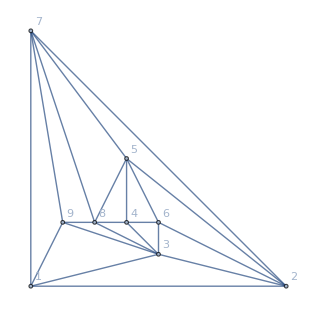

```mathematica
Graph[ReadGrof[41],GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
```

```mathematica
{{"1"<->"2"}, {"3"<->"4"}, {"5"<->"6"}, {"7"<->"8"}, {"1"<->"9"}}
```

```mathematica
Map[{#[[1]]//HexEdge,Framed[Select[#[[2]],SymbolLevel[#]≤4&]]}&,MpgReduce[ReadGrof[40]]]//TableForm
```

1<->2 | {v124x35x689x7,v12x35x47x689,v128x35x47x69,v124x35x67x89,v128x35x49x67}
3<->4 | {v128x349x5x67}
5<->6 | {v128x349x56x7}
7<->8 | {v12x349x56x78}
1<->9 | {v129x34x56x78}

```mathematica
FindFullFormula4[ReadGrof[30]]
```

{v16x278x349x5,v15x28x349x67,v15x278x34x69,v15x278x349x6}

```mathematica
Table[Labeled[Map[{#[[1]]//HexEdge,Framed[Select[#[[2]],SymbolLevel[#]≤4&]]}&,MpgReduce[ReadGrof[k]]]//TableForm,Style[k,Green]],{k,31,50}]
```

{1<->2 | {v128x35x47x69,v1249x35x6x78,v124x35x69x78,v1249x35x67x8,v128x35x49x67}
3<->6 | {v1249x36x5x78}
4<->5 | {v129x36x45x78}
7<->9 | {v128x36x45x79}
3<->1 | {v1236x45x79x8}31,1<->2 | {v128x34x59x67}
3<->7 | {v128x347x59x6}
4<->5 | {v128x37x459x6}
6<->8 | {v12x37x459x68}
1<->9 | {v129x37x45x68}32,1<->2 | {v128x349x5x67}
3<->7 | {v128x347x5x69}
4<->5 | {v128x37x45x69}
6<->8 | {v12x37x45x689}
1<->9 | {v129x37x45x68}33,1<->2 | {v1289x34x5x67}
3<->8 | {v1249x38x5x67}
4<->5 | {v129x38x45x67}
7<->9 | {v12x38x45x679}
1<->6 | {v126x38x45x79}34,1<->2 | {v128x34x56x79,v128x39x47x56,v124x39x56x78,v128x39x45x67}
3<->6 | {v128x36x45x79}
4<->8 | {v1248x36x5x79}
5<->7 | {v1248x36x57x9}
1<->9 | {v129x36x48x57}35,1<->2 | {v125x34x67x89,v128x39x47x56,v124x39x56x78}
3<->5 | {v124x35x67x89}
4<->8 | {v1248x35x67x9}
7<->9 | {v1248x35x6x79}
1<->6 | {v126x35x48x79}36,1<->2 | {v1268x3x479x5,v1268x35x49x7,v124x35x67x89,v128x35x49x67,v1268x35x47x9,v126x35x47x89,v1268x35x4x79,v128x35x479x6,v126x35x479x8,v12x35x479x68,v1268x35x479,v124x35x68x79}
3<->4 | {v1268x34x5x79}
5<->6 | {v128x34x56x79}
7<->8 | {v12x34x56x789}
1<->9 | {v129x34x56x78}37,1<->2 | {v128x36x47x59,v124x35x68x79,v124x35x67x89}
3<->4 | {v128x34x59x67}
5<->6 | {v128x34x56x79}
7<->8 | {v12x34x56x789}
1<->9 | {v129x34x56x78}38,1<->2 | {v124x35x67x89,v128x35x49x67,v124x35x689x7,v12x35x47x689,v128x35x47x69}
3<->4 | {v128x34x59x67}
5<->6 | {v128x34x569x7}
7<->8 | {v12x34x569x78}
1<->9 | {v129x34x56x78}39,1<->2 | {v124x35x689x7,v12x35x47x689,v128x35x47x69,v124x35x67x89,v128x35x49x67}
3<->4 | {v128x349x5x67}
5<->6 | {v128x349x56x7}
7<->8 | {v12x349x56x78}
1<->9 | {v129x34x56x78}40,1<->2 | {v128x35x47x69,v128x35x49x67,v124x37x59x68}
3<->4 | {v128x347x5x69,v128x347x59x6,v12x347x59x68,v128x34x59x67}
5<->6 | {v128x34x569x7,v128x347x56x9,v12x347x569x8,v128x347x569}
7<->8 | {v12x34x569x78}
1<->9 | {v129x34x56x78}41,1<->2 | {v128x35x479x6,v12x35x479x68,v124x35x68x79,v124x35x67x89,v128x35x49x67}
3<->4 | {v128x34x59x67}
5<->6 | {v128x34x56x79}
7<->8 | {v12x34x56x789}
1<->9 | {v129x34x56x78}42,1<->2 | {v124x35x68x79,v1289x35x47x6,v129x35x47x68,v1289x35x4x67,v124x35x67x89}
3<->7 | {v124x37x59x68}
4<->8 | {v1248x37x59x6}
6<->9 | {v1248x37x5x69}
1<->5 | {v125x37x48x69}43,1<->2 | {v128x35x479x6,v12x35x479x68,v124x35x68x79,v124x35x67x89,v128x35x49x67}
3<->4 | {v128x349x5x67}
5<->8 | {v12x349x58x67}
6<->9 | {v12x34x58x679}
1<->7 | {v127x34x58x69}44,1<->2 | {v124x35x689x7,v12x35x47x689,v128x35x47x69,v124x35x67x89,v128x35x49x67}
3<->4 | {v128x349x5x67}
5<->6 | {v128x349x56x7}
7<->8 | {v12x349x56x78}
1<->9 | {v129x34x56x78}45,1<->2 | {v124x38x59x67,v128x35x47x69,v124x37x59x68}
3<->4 | {v128x347x5x69,v128x347x59x6,v12x347x59x68,v128x34x59x67}
5<->6 | {v128x34x569x7,v128x347x56x9,v12x347x569x8,v128x347x569}
7<->8 | {v12x34x569x78}
1<->9 | {v129x34x56x78}46,1<->2 | {v126x3x45x789}
3<->4 | {v126x34x5x789}
5<->7 | {v126x34x57x89}
6<->8 | {v1268x34x57x9}
1<->9 | {v129x34x57x68}47,1<->2 | {v128x3x467x59}
3<->4 | {v128x34x59x67}
5<->7 | {v128x34x579x6}
6<->9 | {v128x34x57x69}
3<->1 | {v1234x57x69x8}48,1<->2 | {v1245x3x67x89,v1245x39x6x78,v1245x39x67x8,v128x39x45x67}
3<->4 | {v125x349x6x78,v128x349x5x67,v125x349x67x8,v125x34x67x89}
5<->7 | {v128x349x57x6}
6<->8 | {v12x349x57x68}
1<->9 | {v129x34x57x68}49,1<->2 | {v128x3x459x67}
3<->4 | {v128x34x59x67}
5<->7 | {v128x34x57x69}
6<->8 | {v12x34x57x689}
1<->9 | {v129x34x57x68}50}